```mathematica
Needs["ExperimentEvaluation`"]
```

```mathematica
labels=Flatten[Outer[StringJoin,{"GPAT3D_","GP3D_"},{"H","H2"}]]
```

{GPAT3D_H,GPAT3D_H2,GP3D_H,GP3D_H2}

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
data=readAllFiles[{"GPAT1D_H099","GPAT1D_H099B","GP1D_H099","GP1D_H099B"}];
```

```mathematica
data=readAllFiles[{"GP4D_E_200","GPAT4D_E_200","GPAT4D_E_200_NOREPEAT","GPAT4D_E_200_TC","GPAT4D_E_200_FULL","GPAT1D_H_100_GP","GP1D_H_100","110813131751_1"},{"GP_E","GPAT_E","GPAT_E_NR","GPAT_E_TC","GPAT_E_GP","GPAT1D_H_100_GP","GP1D_H_100","A"}];
```

```mathematica
keepOnlyBest[{"GP4D_E_200","GPAT4D_E_200","GPAT4D_E_200_GP"},"BSF",5]
```

```mathematica
changingParameters[data]
```

{GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,SOLVER,SYMBOLIC_REGRESSION_1D.A}

```mathematica
sortedData=sortDataByParams[data,{"SYMBOLIC_REGRESSION_1D.F","SYMBOLIC_REGRESSION_1D.A","SOLVER","GPAT.SPECIES_SIZE_MEAN"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
saveData[sortedData,"GP3D_H_H2_200"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","SYMBOLIC_REGRESSION_1D.A","SYMBOLIC_REGRESSION_3D.F","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | SYMBOLIC_REGRESSION_1D.A | SYMBOLIC_REGRESSION_3D.F | GPAT.SPECIES_SIZE_MEAN
12 | GP1D_H099B/parameters_002.txt | GP | 0.1 | NONE | NONE
6 | GPAT1D_H099B/parameters_002.txt | GPAT | 0.1 | NONE | 20.
11 | GP1D_H099B/parameters_001.txt | GP | 0.2 | NONE | NONE
5 | GPAT1D_H099B/parameters_001.txt | GPAT | 0.2 | NONE | 20.
10 | GP1D_H099/parameters_004.txt | GP | 0.3 | NONE | NONE
4 | GPAT1D_H099/parameters_004.txt | GPAT | 0.3 | NONE | 20.
9 | GP1D_H099/parameters_003.txt | GP | 0.5 | NONE | NONE
3 | GPAT1D_H099/parameters_003.txt | GPAT | 0.5 | NONE | 20.
8 | GP1D_H099/parameters_002.txt | GP | 0.9 | NONE | NONE
2 | GPAT1D_H099/parameters_002.txt | GPAT | 0.9 | NONE | 20.
7 | GP1D_H099/parameters_001.txt | GP | 3. | NONE | NONE
1 | GPAT1D_H099/parameters_001.txt | GPAT | 3. | NONE | 20.

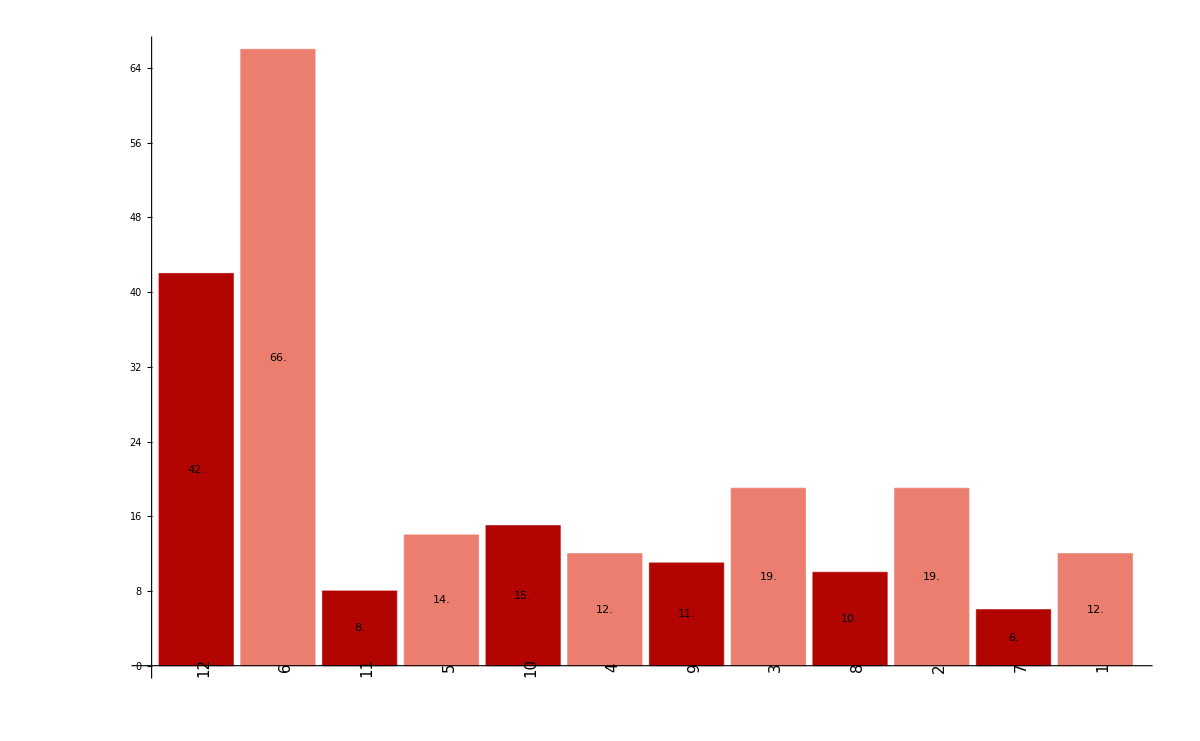

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",2]
```

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSF"];
```

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GPAT_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[sortedData,"12","6","SUCCESS",TwoSided->True]
```

| 12 | 6
true | 42. | 66.
false | 58. | 34.

0.00104976

```mathematica
sortConfigurationResults[sortedData,"A","BSF",10]
```

1 | 0.996687
12 | 0.983575
100 | 0.970368
78 | 0.96933
10 | 0.968461
60 | 0.968217
79 | 0.963918
73 | 0.958339
68 | 0.956159
35 | 0.955737

```mathematica
Expand[1.5*x1*x2+2.3*x1+x2*x3*x4-1.1*x3]
```

2.3 x1+1.5 x1 x2-1.1 x3+x2 x3 x4

```mathematica
(res=sortConfigurationResults[sortedData,"GP3D_H2","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {x_2 (-1.+x_1 (x_3+x_2 x_3))} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+x_1 x_3+x_1 x_2 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_2 (x_1+x_1 x_2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1 x_2^2 x_3+x_2 (-1.+x_1 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1-1. x_2+x_1 (-1.+x_2 x_3+x_2^2 x_3)} | {0.-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+(x_1+x_1 x_2) x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {1.08185×10^-8-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {1.08185×10^-8-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 (4.44373×10^-11+x_2 x_3+x_2^2 x_3)} | {4.44373×10^-11 x_1-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.

```mathematica
(res=sortConfigurationResults[sortedData,"12","BSF",25,Output->"Expressions"]/.{x0->x})
```

Gen | Expression | Expanded | f
last | {0.09977 x (x+Sin[0.787112 ⅇ^(-x^2)])} | {0.09977 x^2+0.09977 x Sin[0.787112 ⅇ^(-x^2)]} | 0.995529
last | {0.0646032 x (ⅇ^(-x^2)+1.55385 x)-0.0344501 Sin[1.-ⅇ^(-x^2)]} | {0.0646032 ⅇ^(-x^2) x+0.100383 x^2-0.0344501 Sin[1.-ⅇ^(-x^2)]} | 0.995316
last | {0.100061 x (0.0156719+x)} | {0.00156814 x+0.100061 x^2} | 0.995278
last | {ⅇ^(-11.8063-Sin[x]^2)+0.0999739 x (0.021377+x)} | {ⅇ^(-11.8063-Sin[x]^2)+0.00213714 x+0.0999739 x^2} | 0.995253
last | {0.100195 x^2} | {0.100195 x^2} | 0.995163
last | {0.0997882 x^2} | {0.0997882 x^2} | 0.995147
last | {-0.0015477+0.100253 x^2} | {-0.0015477+0.100253 x^2} | 0.995127
last | {0.0995871 x^2} | {0.0995871 x^2} | 0.994844
last | {0.0995752 x^2} | {0.0995752 x^2} | 0.99482
last | {0.100443 x^2} | {0.100443 x^2} | 0.994783
last | {0.0999352 (-0.0328145+x) x} | {-0.00327932 x+0.0999352 x^2} | 0.994597
last | {0.0994062 x^2} | {0.0994062 x^2} | 0.994405
last | {0.100651 x^2} | {0.100651 x^2} | 0.994233
last | {4.35401×10^-11+0.100887 x (ⅇ^(-x^2)+x)} | {4.35401×10^-11+0.100887 ⅇ^(-x^2) x+0.100887 x^2} | 0.993847
last | {0.10084 x^2} | {0.10084 x^2} | 0.993554
last | {0.0993273 x (ⅇ^(-33.9284 (3.47822+x)^2)+x)} | {0.0993273 ⅇ^(-33.9284 (3.47822+x)^2) x+0.0993273 x^2} | 0.993273
last | {0.0990122 x^2} | {0.0990122 x^2} | 0.992907
last | {-0.000371379+0.0990141 x^2} | {-0.000371379+0.0990141 x^2} | 0.992889
last | {Sin[0.129682 x] (x-Sin[0.336709 x]-0.196058 Sin[x])} | {x Sin[0.129682 x]-Sin[0.129682 x] Sin[0.336709 x]-0.196058 Sin[0.129682 x] Sin[x]} | 0.992606
last | {0.101464 (-0.763579+x (0.0208029+x))} | {-0.0774756+0.00211074 x+0.101464 x^2} | 0.992428
last | {0.0988539 x^2} | {0.0988539 x^2} | 0.992097
last | {0.101382 x (ⅇ^(-0.332217 x^2)+x)} | {0.101382 ⅇ^(-0.332217 x^2) x+0.101382 x^2} | 0.99195
last | {(0.815193 x^2 (-0.632121 ⅇ^(-(4.80488+x)^2)+x+ⅇ^(-x^2) (2.03518+x)) ArcTan[x])/(√(1+140.445 x^2))} | {(1.65907 ⅇ^(-x^2) x^2 ArcTan[x])/(√(1+140.445 x^2))-(0.5153 ⅇ^(-(4.80488+x)^2) x^2 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 x^3 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 ⅇ^(-x^2) x^3 ArcTan[x])/(√(1+140.445 x^2))} | 0.991336
last | {0.10128 x^2} | {0.10128 x^2} | 0.991321
last | {0.0989743 x (0.0785205+x)} | {0.00777151 x+0.0989743 x^2} | 0.991136

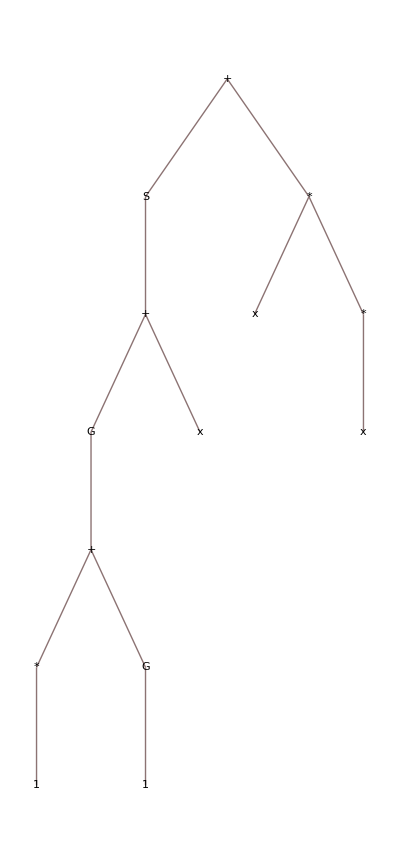
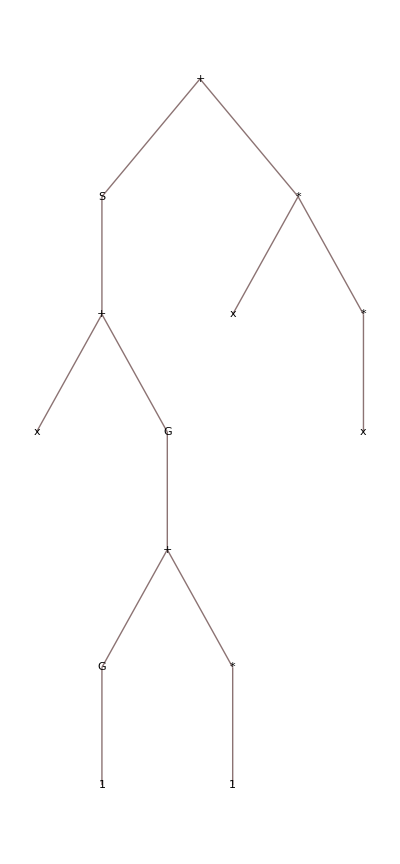
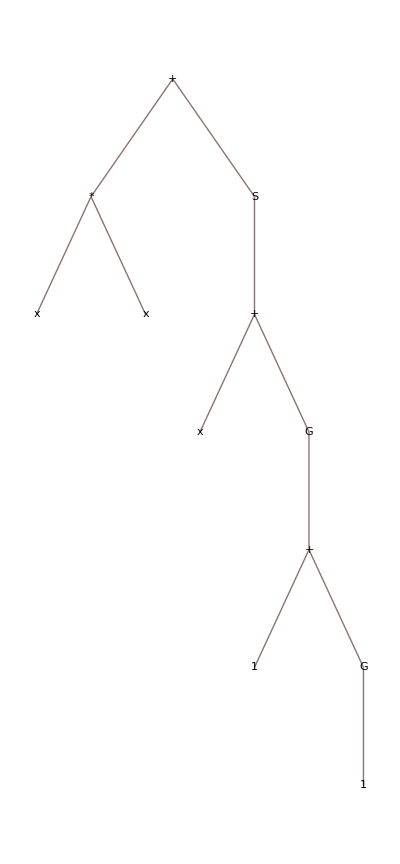
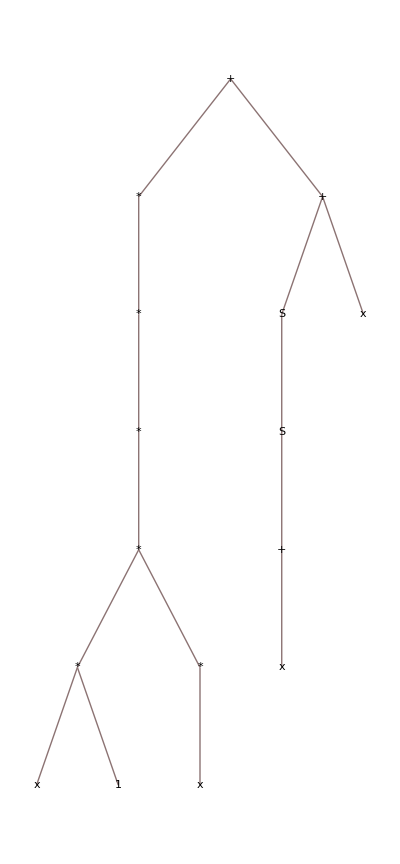
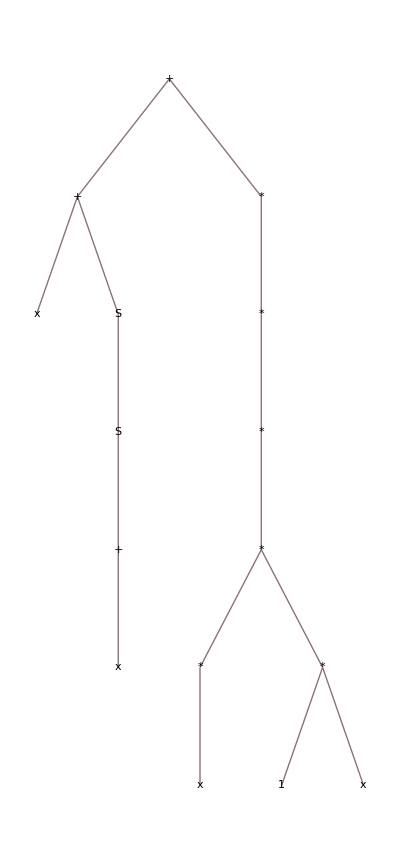
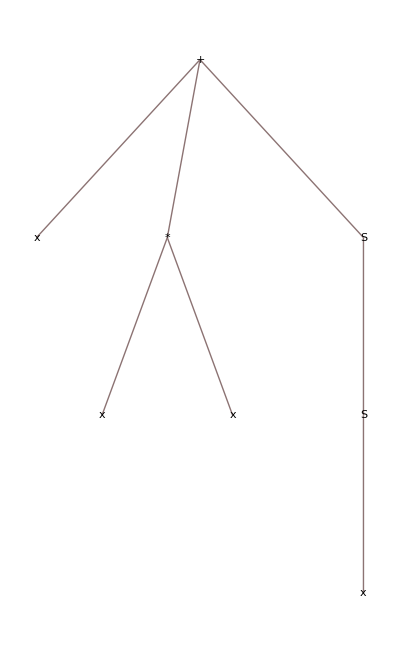
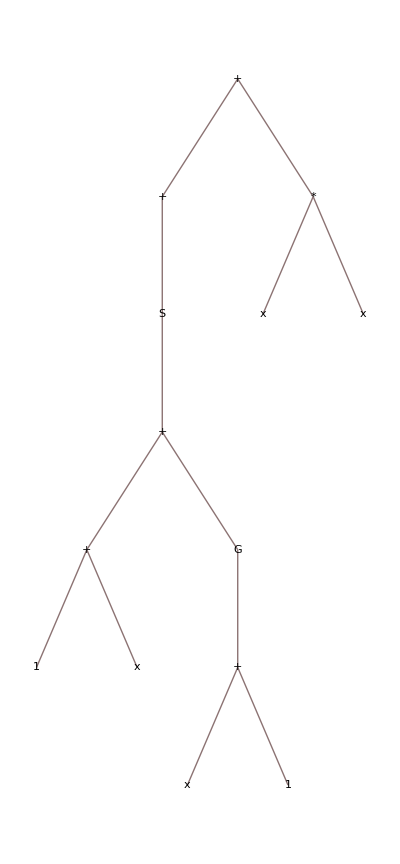
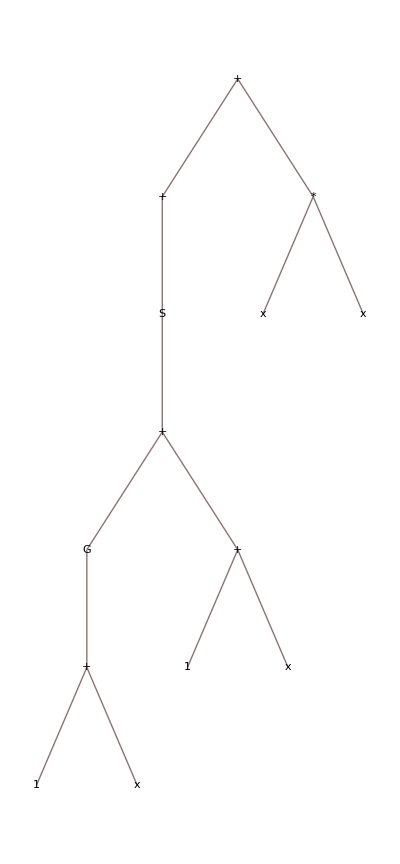
Gen | Genome | Sorted | Simplified | f
last | -Graphics- | -Graphics- | -Graphics- | 0.99656
last | -Graphics- | -Graphics- | -Graphics- | 0.983261
last | -Graphics- | -Graphics- | -Graphics- | 0.978954
last | -Graphics- | -Graphics- | -Graphics- | 0.978529
last | -Graphics- | -Graphics- | -Graphics- | 0.957386
last | -Graphics- | -Graphics- | -Graphics- | 0.956843
last | -Graphics- | -Graphics- | -Graphics- | 0.952837
last | -Graphics- | -Graphics- | -Graphics- | 0.951168
last | -Graphics- | -Graphics- | -Graphics- | 0.940757
last | -Graphics- | -Graphics- | -Graphics- | 0.852304

```mathematica
(res=sortConfigurationResults[sortedData,"A","BSF",10,Output->"BSFGenomes"]/.{x0->x})
```

```mathematica
Export["GP_H2.pdf",%]
```

GP_H2.pdf